# Задание 10.

## Методы Монте-Карло

## Мосейков Игнатий Геннадьевич, группа 21372

## Задание

Все задачи в этом задании взяты из методического пособия Войтишек А.В. Лекции по численным методам Монте-Карло (ссылка). В пособии эти задачи разобраны. Вам нужно выполнить (воспроизвести с помощью системы Wolfram Mathematica) математические выкладки, реализовать генераторы, построить гистограммы и плотности распределения.

### [раздел 6.5] Индикатриса Хеньи-Гринстейна (Метод обратной функции распределения)

При численном решении задач теории переноса излучения широко используется индикатриса Хеньи-Гринстейна, представляющая собой плотность распределения косинуса угла рассеяния  u при столкновении “фотона” с частицей среды cледующего вида

f(u)=(1-μ^2)/(2(1+μ^2-2μ u)^(3/2)), u∈(-1,+1)

Плотность распределения зависит от параметра  μ∈(-1,1). Постройте метод генерации u в соответствии с эти распределением, постройте гистограммы + графики  плотностей распределения при разных μ (графики могут быть интерактивными).

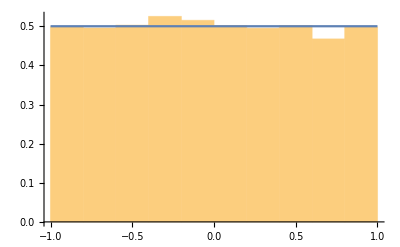

```mathematica
f[mu_,u_]:=(1-mu^2)/(2*(1+mu^2-2*mu*u)^(3/2));
createGenU[genU_,mu_]:=Module[
{normU,eq,res,U},normU=Integrate[f[mu,t],{t,-1,1}];
eq=Integrate[f[mu,t]/normU,{t,-1,U},Assumptions->U>-1&&U<1&&mu>-1&&mu<1];
res[val_]:=First[U/.Solve[eq==val,U,InverseFunctions->True]];
genU[]:=res[RandomReal[]]
];
mu = 0;
createGenU[genU,mu]
Show[Histogram[Table[genU[],{i,10^4}],10,"PDF"],Plot[f[mu,u],{u,-1,1}]]
```

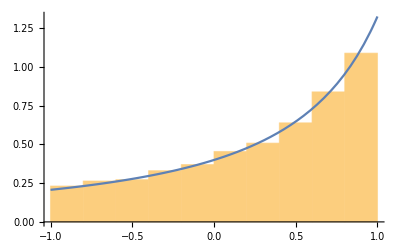

```mathematica
mu = 0.3;
createGenU[genU,mu]
Show[Histogram[Table[genU[],{i,10^4}],10,"PDF"],Plot[f[mu,u],{u,-1,1}]]
```

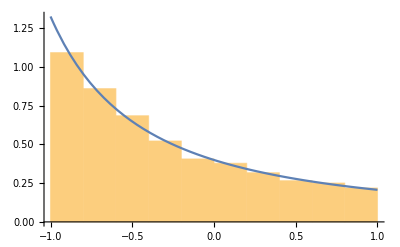

```mathematica
mu = -0.3;
createGenU[genU,mu]
Show[Histogram[Table[genU[],{i,10^4}],10,"PDF"],Plot[f[mu,u],{u,-1,1}]]
```

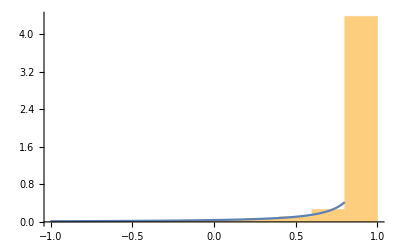

```mathematica
mu = 0.9;
createGenU[genU,mu]
Show[Histogram[Table[genU[],{i,10^4}],10,"PDF"],Plot[f[mu,u],{u,-1,1}]]
```

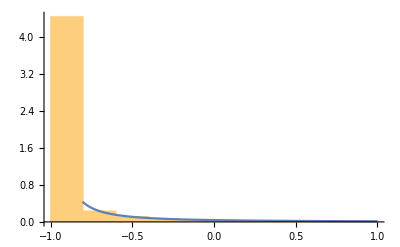

```mathematica
mu = -0.9;
createGenU[genU,mu]
Show[Histogram[Table[genU[],{i,10^4}],10,"PDF"],Plot[f[mu,u],{u,-1,1}]]
```

### [Пример Б2] (Конструирование двумерного моделируемого вектора с зависимыми координатами)

Сформулируйте стандартный метод моделирования случайного вектора и продемонстрируйте его на примере двумерного вектора (ξ, η), имеющего плотность распределения. Постройте 2-мерные гистограмму + плотность распределения.

f(u,v)=3 u^2(u+1)v^u e^(-u^3),  0<u<∞, 0<v<1

```mathematica
fuv[u_,v_]:=3u^2(u+1)v^u*Exp[-u^3];
```

```mathematica
createGenV[genV_]:=Module[
{fu,fvu,eqU,U,eqV,V,resU,resV,resu,resv},
fu[u_]:=Integrate[fuv[u,v],{v,0,1},Assumptions->u>0];
fvu[v_,u_]:=fuv[u,v]/fu[u];
eqU=Integrate[fu[u],{u,0,U},Assumptions->Element[U,Reals]];
eqV=Integrate[fvu[v,U],{v,0,V},Assumptions->Element[U,Reals]&&Element[V,Reals]];
resU[val_]:=U/.(Solve[eqU==val&&Re[U]>0,U,Reals])[[1]];
resV[val_]:=V/.(Solve[(eqV/.U->resu)==val&&Re[V]<1&&Re[V]>0,V,Reals])[[1]];
genV[]:=(
resu=resU[RandomReal[]];
resv=resV[RandomReal[]];
{resu,resv}
);
];
```

```mathematica
createGenV[genV];
genV[]
```

{1.10096,0.706643}

```mathematica
Show[Histogram3D[Table[genV[],{i,10^4}],{{0.1},{0.05}},"PDF",AxesLabel->{u,v}],
Plot3D[fuv[u,v],{u,0,3},{v,0,1}]]
```

-Graphics3D-

### [Пример В6] (Метод дискретной суперпозиции)

Требуется построить алгоритм моделирования случайной величины ξ, имеющей плотность распределения.

f(u)=(5u)/((1+u^2)^2)+(√2 π)/(8 u^2)sin(π/(2u)), 1<u<2

```mathematica
f1[u_]:=5u/((1+u^2)^2);
f2[u_]:=Sqrt[2]*Pi*Sin[Pi/(2u)]/(8u^2);
```

```mathematica
createGenDiscreteSuperposition[genDiscreteSuperposition_]:=Module[
{p1,p2,F1,F2,U,res1,res2, val},
p1=Integrate[f1[u],{u,1,2}];
p2=Integrate[f2[u],{u,1,2}];
F1=Integrate[f1[u]/p1,{u,1,U}];
F2=Integrate[f2[u]/p2,{u,1,U}];
res1:=U/.Solve[F1==val&&Re[U]>1&&Re[U]<2,U,Reals][[1]];

res2:=U/.Solve[F2==val&&Re[U]>1&&Re[U]<2,U,Reals][[1]];
genDiscreteSuperposition[]:=If[RandomReal[]<=p1,res1/.val->RandomReal[],res2/.val->RandomReal[]];
];
```

```mathematica
createGenDiscreteSuperposition[genDiscreteSuperposition]
genDiscreteSuperposition[]
```

1.2888

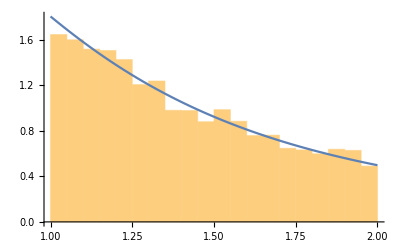

```mathematica
Show[Histogram[Table[genDiscreteSuperposition[],{i,10^4}],20,"PDF"],Plot[f1[u]+f2[u],{u,1,2}]]
```

### [Пример Г4] (Метод исключения)

Рассмотрим случайную величину ξ, имеющую плотность распределения (lg - десятичный логарифм)

f(u)=1/(Ḡ(u^2 lg(u+10)+10)), 0 < u <1

Нормировка плотности распределения в элементарных функциях не вычисляется

Ḡ=(∫_0)^1 ⅆu/(u^2 lg(u+10)+10)

Реализуйте алгоритм метода исключения для этой случайной величины.

Как только у вас будет генератор вы можете оценить интеграл Ḡ методом Монте-Карло (как?). Оцените погрешность оценки Ḡ методом Монте-Карло. Как ведет себя погрешность с увеличением n числа разыгранных случайных величин (попробуйте n = 10, 100, 1000, 10000).

Сравните со значением Ḡ, которое дает NIntegrate.

Постройте гистограмму и плотность распределения.

```mathematica
g[u_]:=1/(u^2*Log10[u+10]+10);
G=NIntegrate[g[u],{u,0,1}];
g1[u_]:=1/(u^2+10);
```

0.947532

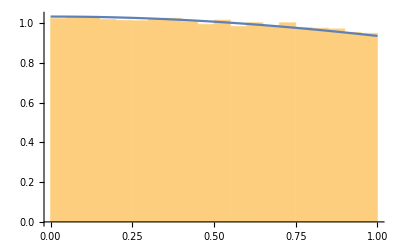

```mathematica
makeGenElimination[genElimination_]:=Module[{G1,U,F1,res, val, xi0,nu0},
G1=Integrate[g1[u],{u,0,1}];
F1=Integrate[g1[u]/G1,{u,0,U}];
res=U/.Solve[F1==val,U,Reals][[1]];
genElimination[]:=(
xi0=res/.val->RandomReal[];
nu0=RandomReal[]*g1[xi0];
If[nu0<g[xi0],xi0,genElimination[]]
);
];
makeGenElimination[genElimination];
genElimination[]
Show[Histogram[Table[genElimination[],{i,10^5}],20,"PDF"],Plot[g[u]/G,{u,0,1}]]
```

```mathematica
GSet = Table[g[RandomReal[]],{i,10^5}];
G
```

0.0967616

```mathematica
Print["N=10: ",Mean[GSet],"+-",Sqrt[Variance[GSet]/10]]
```

N=10: 0.0967489+-0.000902358

```mathematica
Print["N=100: ",Mean[GSet],"+-",Sqrt[Variance[GSet]/10^2]]
```

N=100: 0.0967489+-0.000285351

```mathematica
Print["N=1000: ",Mean[GSet],"+-",Sqrt[Variance[GSet]/10^3]]
```

N=1000: 0.0967489+-0.0000902358

```mathematica
Print["N=10000: ",Mean[GSet],"+-",Sqrt[Variance[GSet]/10^4]]
```

N=10000: 0.0967489+-0.0000285351

### [Пример Д3] (Выборка по важности)

Реализуйте алгоритм выборки по важности для вычисления 4-кратного интеграла. Оцените дисперсию оценки интеграла. Попробуйте сравнить со встроенной функцией NIntegrate  (с разными стратегиями интегрирования и опциями вычислений)

I=(∫_0)^1 ⅆ x_1∫_0^1 ⅆ x_2(∫_(-∞))^(+∞)ⅆ x_3(∫_(-∞))^(+∞)ⅆ x_4(x_1^3 x_2)/((x_1^4+1)^2)ⅇ^(-(2 x_2^2+x_3^2+x_4^2)/2)√(1+(7 sin^4(x_1 x_2 x_3 x_4))/9)

```mathematica
genIntegral[]:=Module[
{a1,a2,a3,a4,xi1,xi2,xi3,xi4},
a1=RandomReal[];
a2=RandomReal[];
a3=RandomReal[];
a4=RandomReal[];
xi1=Power[a1/(2-a1),1/4];
xi2=Sqrt[-Log[1-a2(1-Exp[-1/2])]];
xi3=Sqrt[-2Log[a3]]Sin[2Pi*a4];
xi4=Sqrt[-2Log[a3]]Cos[2Pi*a4];
Sqrt[1+7Power[Sin[xi1*xi2*xi3*xi4],4]/9]/Pi*2*(1-Exp[-1/2])
];
Mean[Table[genIntegral[],{i,10^5}]]
```

0.253984

```mathematica
Variance[Table[genIntegral[],{i,10^5}]]
```

0.000137071

```mathematica
NIntegrate[(x1^3)/((x1^4+1)^2)*x2*Exp[-(2x2^2+x3^2+x4^2)/2]*Sqrt[1+7Power[Sin[x1*x2*x3*x4],4]/9],{x1,0,1},{x2,0,1},{x3,-Infinity,Infinity},{x4,-Infinity,Infinity}]
```

0.253874